```mathematica
ΔzFixed=1.0927272727272728;
```

# Preliminaries

```mathematica
CChop[x_]:=Chop[N@x,10^-3 Abs@x]
```

## ‘Sensical’ constraints

```mathematica
SensicalConstraints[{t1Input_},{m12_,s2Input_},{σ34_,ρ3_},{z4Input_},{μ5_,z5Input_},{timInput_},{zm1Input_},sCelestial_]:=
Module[
{
t0,s0,z0,t1,s1,z1,t2,s2,z2,t3,s3,z3,t4,s4,z4,t5,s5,z5,tim,sim,zim,tm1,sm1,zm1,ti0,si0,zi0
},

t0=10^-10;
s0=10^-10;
z0=10^-10;

t1=t1Input;
s1=10^-10;
z1=10^-10;

t2=m12 z2+t1;
s2=s2Input;
z2=s2/Sqrt[24];

t3=(t4-t2)/(z4-z2)z3+(t2-(t4-t2)/(z4-z2) z2);
s3=σ34 s4;
z3=z2+ρ3(z4-z2);

t4=t5+z5-z4;
s4=sCelestial;
z4=z4Input;

t5=μ5 z5;
s5=sCelestial;
z5=z5Input;

tim=timInput;
sim=10^-10;
zim=10^-10;

tm1=tim+zm1;
sim=sCelestial;
zm1=zm1Input;

ti0=1/2 (t5+tim+z5);
si0=10^-10;
zi0=1/2 (t5-tim+z5);

And[
z1<=z2<=z3<=z4<=z5<=zi0,
ti0<=t5<=t4,
tim<=tm1,
Abs[(t4-t2)/(z4-z2)]<=1
]
]
```

## Visualization of Geometry

```mathematica
GeometryVisualization[{t1Input_},{m12_,s2Input_},{σ34_,ρ3_},{z4Input_},{μ5_,z5Input_},{timInput_},{zm1Input_},sCelestial_]:=
Module[
{
t0,s0,z0,t1,s1,z1,t2,s2,z2,t3,s3,z3,t4,s4,z4,t5,s5,z5,tim,sim,zim,tm1,sm1,zm1,ti0,si0,zi0
},

t0=10^-10;
s0=10^-10;
z0=10^-10;

t1=t1Input;
s1=10^-10;
z1=10^-10;

t2=m12 z2+t1;
s2=s2Input;
z2=(*s2/Sqrt[24]*)1/(1+s2);

t3=(t4-t2)/(z4-z2)z3+(t2-(t4-t2)/(z4-z2) z2);
s3=σ34 s4;
z3=z2+ρ3(z4-z2);

t4=t5+z5-z4;
s4=sCelestial;
z4=z4Input;

t5=μ5 z5;
s5=sCelestial;
z5=z5Input;

tim=timInput;
sim=10^-10;
zim=10^-10;

tm1=tim+zm1;
sim=sCelestial;
zm1=zm1Input;

ti0=1/2 (t5+tim+z5);
si0=10^-10;
zi0=1/2 (t5-tim+z5);

Graphics@Module[
{
vertices=
{{z0,t0},{z1,t1},{z2,t2},{z3,t3},{z4,t4},{z5,t5},{zi0,ti0},{zm1,tm1},{zim,tim}}
},
Join[
Line@#&/@Table[
{vertices[[i]],vertices[[Mod[i+1,9,1]]]},
{i,Length@vertices}
],
Point@#&/@vertices
]
]
]
```

## Boundary conditions and parameters

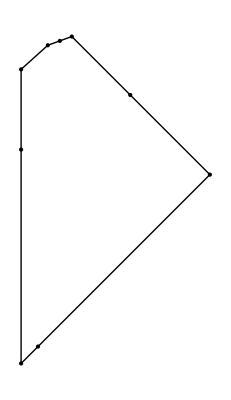

```mathematica
t1Fixed=1.5;
m12Fixed=0.9;
σ34Fixed=0.9;
ρ3Fixed=0.5;
μ5Fixed=0.5;
z5Fixed=sCelestialFixed/Sqrt[24];
timFixed=-4;
zm1Fixed=0.316;
sCelestialFixed=10;

z4Fixed=z5Fixed-ΔzFixed;

ΩFixed=10^0;
GFixed=(*10^1.7*)10^0.3;

ϵFixed=10^-3;

nBFixed=1.0001;

Module[
{t1Input,
m12,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial
},
t1Input=t1Fixed;

m12=m12Fixed;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

GeometryVisualization[{t1Input},{m12,1},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial]
]
```

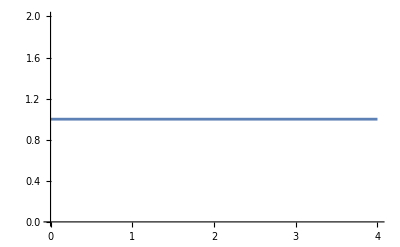

```mathematica
Module[
{t1Input,
m12,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial
},
t1Input=t1Fixed;

m12=m12Fixed;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

Plot[
Boole@SensicalConstraints[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial],
{s2,0,4}
]
]
```

# Hawking

```mathematica
SlopeHawking[{t1Input_},{m12_,s2Input_},{σ34_,ρ3_},{z4Input_},{μ5_,z5Input_},{timInput_},{zm1Input_},sCelestial_,{Ωim_,Ωm1_,Ωi0_},G_,n_,ϵ_]:=
1/ϵ Re[
ReducedSemiclassicalHawkingW[{t1Input},{m12,s2Input+ϵ},{σ34,ρ3},{z4Input},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,n]-ReducedSemiclassicalHawkingW[{t1Input},{m12,s2Input},{σ34,ρ3},{z4Input},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,n]
]
```

## Saddle search

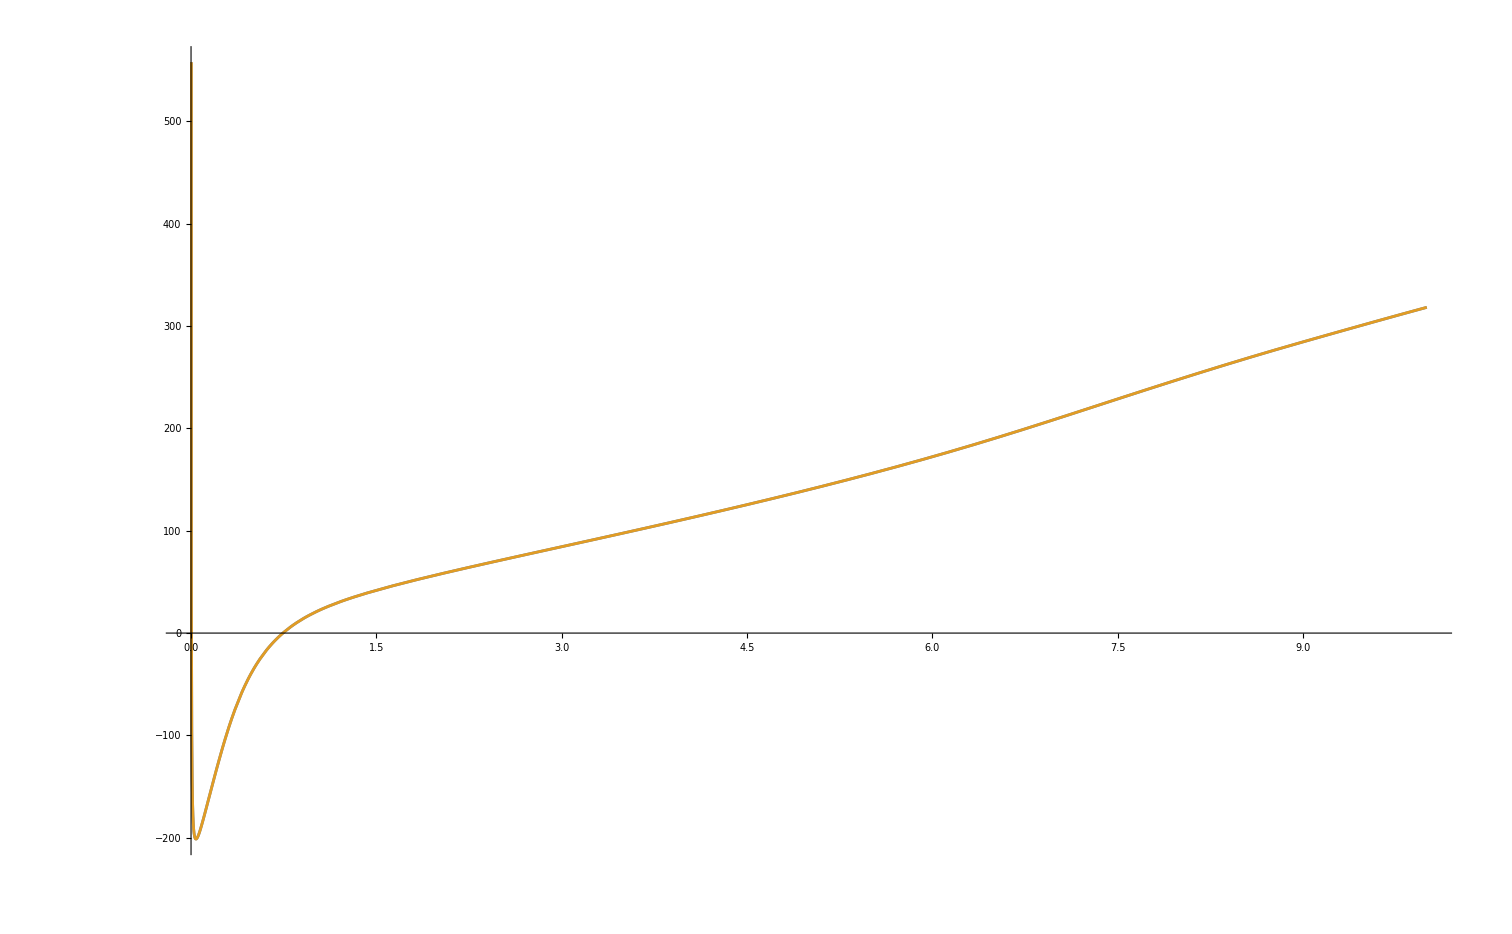

```mathematica
Module[
{t1Input,
m12,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial,
Ωim,Ωm1,Ωi0,
G,
nB,
ϵ
},
t1Input=t1Fixed;

m12=m12Fixed;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

Ωim=ΩFixed;
Ωm1=ΩFixed;
Ωi0=ΩFixed;

G=GFixed;
nB=nBFixed;

ϵ=ϵFixed;

Plot[
{
SlopeHawking[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,1,ϵ],
SlopeHawking[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,nB,ϵ]
},
{s2,0,10}
]
]
```

```mathematica
saddleRegimeH="Second";
s2SeedHnA=0.75;
s2SeedHnB=0.75;
```

```mathematica
Module[
{t1Input,
m12,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial,
Ωim,Ωm1,Ωi0,
G,
nB,
ϵ
},
t1Input=t1Fixed;

m12=m12Fixed;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

Ωim=ΩFixed;
Ωm1=ΩFixed;
Ωi0=ΩFixed;

G=GFixed;
nB=nBFixed;

ϵ=ϵFixed;

TimeConstrained[
FindRoot[
{SlopeHawking[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,1,ϵ]==0},
{s2,s2SeedHnA}
],
120
]
]
s2HnA=%[[1,2]];;
```

{s2→0.743575}

```mathematica
Module[
{t1Input,
m12,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial,
Ωim,Ωm1,Ωi0,
G,
nB,
ϵ
},
t1Input=t1Fixed;

m12=m12Fixed;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

Ωim=ΩFixed;
Ωm1=ΩFixed;
Ωi0=ΩFixed;

G=GFixed;
nB=nBFixed;

ϵ=ϵFixed;

TimeConstrained[
FindRoot[
{SlopeHawking[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,nB,ϵ]==0},
{s2,s2SeedHnB}
],
120
]
]
s2HnB=%[[1,2]];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{s2→0.743575}

## Results

```mathematica
WHnA=Module[
{t1Input,
m12,s2,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial,
Ωim,Ωm1,Ωi0,
G,
nB,
ϵ
},
t1Input=t1Fixed;

m12=m12Fixed;
s2=s2HnA;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

Ωim=ΩFixed;
Ωm1=ΩFixed;
Ωi0=ΩFixed;

G=GFixed;
nB=nBFixed;

ϵ=ϵFixed;

ReducedSemiclassicalHawkingW[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,1]
]
```

3995.13+6.14798×10^-17 ⅈ

```mathematica
WHnB=Module[
{t1Input,
m12,s2,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial,
Ωim,Ωm1,Ωi0,
G,
nB,
ϵ
},
t1Input=t1Fixed;

m12=m12Fixed;
s2=s2HnB;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

Ωim=ΩFixed;
Ωm1=ΩFixed;
Ωi0=ΩFixed;

G=GFixed;
nB=nBFixed;

ϵ=ϵFixed;

ReducedSemiclassicalHawkingW[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,nB]
]
```

3995.52-0.00031543 ⅈ

```mathematica
SH=-1/(n-1)(CChop@WHnB-n CChop@WHnA)/.n->nBFixed
```

105.041

```mathematica
s2HnB
```

0.743575

```mathematica
{ΔzFixed,s2HnB,SH}
```

{1.09273,0.743575,105.041}

# Wormhole

```mathematica
SlopeWormhole[{t1Input_},{m12_,s2Input_},{σ34_,ρ3_},{z4Input_},{μ5_,z5Input_},{timInput_},{zm1Input_},sCelestial_,{Ωim_,Ωm1_,Ωi0_},G_,n_,ϵ_]:=
1/ϵ Re[
ReducedSemiclassicalWormholeW[{t1Input},{m12,s2Input+ϵ},{σ34,ρ3},{z4Input},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,n]-ReducedSemiclassicalWormholeW[{t1Input},{m12,s2Input},{σ34,ρ3},{z4Input},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,n]
]
```

## Saddle search

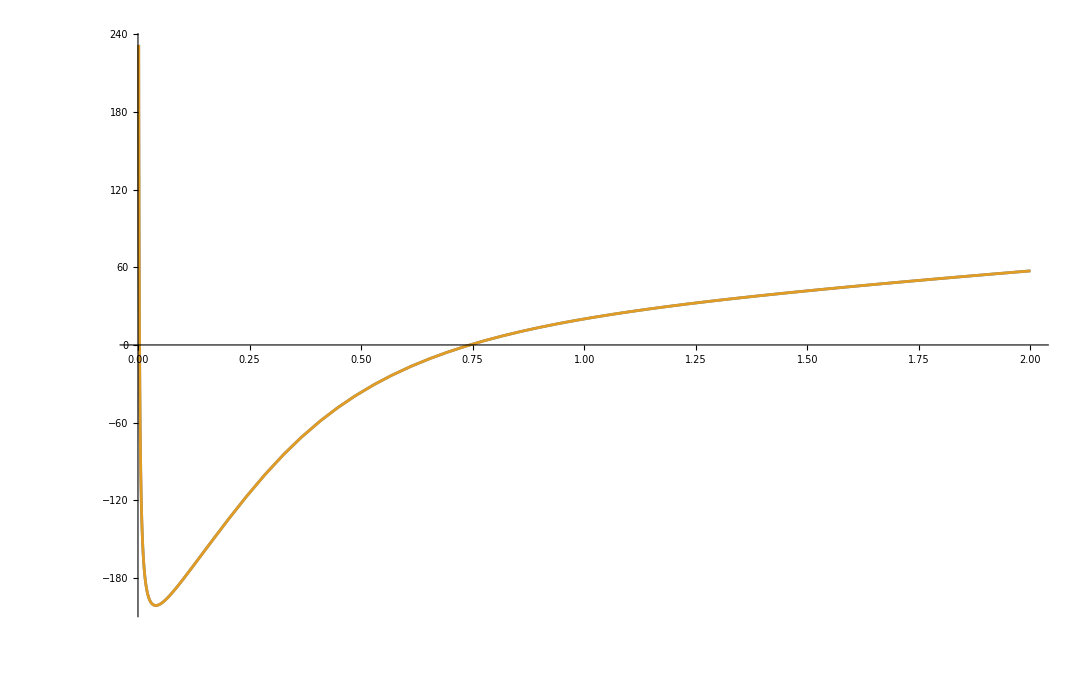

```mathematica
Module[
{t1Input,
m12,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial,
Ωim,Ωm1,Ωi0,
G,
nB,
ϵ
},
t1Input=t1Fixed;

m12=m12Fixed;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

Ωim=ΩFixed;
Ωm1=ΩFixed;
Ωi0=ΩFixed;

G=GFixed;
nB=nBFixed;

ϵ=ϵFixed;

Plot[
{
SlopeWormhole[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,1,ϵ],
SlopeWormhole[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,nB,ϵ]
},
{s2,0,2}
]
]
```

```mathematica
saddleRegimeW="Second";
s2SeedWnA=0.75;
s2SeedWnB=0.75;
```

```mathematica
Module[
{t1Input,
m12,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial,
Ωim,Ωm1,Ωi0,
G,
nB,
ϵ
},
t1Input=t1Fixed;

m12=m12Fixed;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

Ωim=ΩFixed;
Ωm1=ΩFixed;
Ωi0=ΩFixed;

G=GFixed;
nB=nBFixed;

ϵ=ϵFixed;

TimeConstrained[
FindRoot[
{SlopeWormhole[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,1,ϵ]==0},
{s2,s2SeedWnA}
],
120
]
]
s2WnA=%[[1,2]];;
```

{s2→0.743584}

```mathematica
Module[
{t1Input,
m12,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial,
Ωim,Ωm1,Ωi0,
G,
nB,
ϵ
},
t1Input=t1Fixed;

m12=m12Fixed;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

Ωim=ΩFixed;
Ωm1=ΩFixed;
Ωi0=ΩFixed;

G=GFixed;
nB=nBFixed;

ϵ=ϵFixed;

TimeConstrained[
FindRoot[
{SlopeWormhole[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,nB,ϵ]==0},
{s2,s2SeedWnB}
],
120
]
]
s2WnB=%[[1,2]];;
```

{s2→0.743586}

## Results

```mathematica
WWnA=Module[
{t1Input,
m12,s2,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial,
Ωim,Ωm1,Ωi0,
G,
nB,
ϵ
},
t1Input=t1Fixed;

m12=m12Fixed;
s2=s2WnA;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

Ωim=ΩFixed;
Ωm1=ΩFixed;
Ωi0=ΩFixed;

G=GFixed;
nB=nBFixed;

ϵ=ϵFixed;

ReducedSemiclassicalWormholeW[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,1]
]
```

3995.14+6.12702×10^-17 ⅈ

```mathematica
WWnB=Module[
{t1Input,
m12,s2,
σ34,ρ3,
z4,
μ5,z5Input,
timInput,
zm1Input,
sCelestial,
Ωim,Ωm1,Ωi0,
G,
nB,
ϵ
},
t1Input=t1Fixed;

m12=m12Fixed;
s2=s2WnB;

σ34=σ34Fixed;
ρ3=ρ3Fixed;

z4=z4Fixed;

μ5=μ5Fixed;
z5Input=z5Fixed;

timInput=timFixed;

zm1Input=zm1Fixed;

sCelestial=sCelestialFixed;

Ωim=ΩFixed;
Ωm1=ΩFixed;
Ωi0=ΩFixed;

G=GFixed;
nB=nBFixed;

ϵ=ϵFixed;

ReducedSemiclassicalWormholeW[{t1Input},{m12,s2},{σ34,ρ3},{z4},{μ5,z5Input},{timInput},{zm1Input},sCelestial,{Ωim,Ωm1,Ωi0},G,nB]
]
```

3995.53-0.000314354 ⅈ

```mathematica
SW=-1/(n-1)(CChop@WWnB-n CChop@WWnA)/.n->nBFixed
```

105.04

```mathematica
s2WnB
```

0.743586

```mathematica
{ΔzFixed,s2WnB,SW}
```

{1.09273,0.743586,105.04}

# Final results

## Hawking

```mathematica
{ΔzFixed,s2HnB,SH}
```

{1.09273,0.743575,105.041}

## Wormhole

```mathematica
{ΔzFixed,s2WnB,SW}
```

{1.09273,0.743586,105.04}

```mathematica
EmitSound[Sound[SoundNote[]]]
```